```mathematica
usbcs={"adcirc_flow","adcirc_stage","rdhm_flow"};
dsbcs={"adcirc_stage","stage_0","noriver_adcirc_stage"};
sites={"greenville","rock_springs","grimesland"};
```

```mathematica
hecplot["Floyd", "rivers_on", "fine_grid", "rock_springs", 
  "flow", False, Blue]
```

Part::partw: Part 1 of {} does not exist.

ToExpression::notstrbox: {} ⟦ 1 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 2 of {} does not exist.

ToExpression::notstrbox: {} ⟦ 2 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ToExpression::notstrbox: {} ⟦ 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Table::iterb: Iterator {time, start, end, 604800} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Union::normal: Nonatomic expression expected at position 1 in Union[obflowscatter].

ListPlot::prng: Value of option PlotRange -> {{start, end}, {-1000 + $Failed, 1000 + $Failed}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: obflowscatter is not a list of numbers or pairs of numbers.

Union::normal: Nonatomic expression expected at position 1 in Union[obflowscatter].

ListPlot::prng: Value of option PlotRange -> {{start, end}, {-1000 + $Failed, 1000 + $Failed}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: obflowscatter is not a list of numbers or pairs of numbers.

Union::normal: Nonatomic expression expected at position 1 in Union[obflowscatter].

General::stop: Further output of Union :: normal will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{start, end}, {-1000 + $Failed, 1000 + $Failed}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot :: prng will be suppressed during this calculation.

ListPlot::lpn: obflowscatter is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot[hecflowscatter,Joined→True,PlotRange→{{start,end},{-1000+$Failed,1000+$Failed}},Frame→True,FrameTicks→{{Automatic,None},{Table[{time+60 60 12 7,DateString[time+60 60 12 7,{MonthShort,/,DayShort}]},{time,start,end,604800}],None}},FrameLabel→{{cfs,None},{Date, GMT,title}},GridLines→{Table[time+60 60 12 7,{time,start,end,604800}],Automatic},BaseStyle→{FontSize→14,FontFamily→Times New Roman},ImageSize→Large,PlotStyle→-Graphics-]

```mathematica
Quiet[




s1=Show[
 hecplot["irene", "rdhm_flow", "adcirc_stage", "rock_springs", 
  "stage", False, Blue],
 hecplot["irene", "rdhm_flow", "noriver_adcirc_stage", "rock_springs",
   "stage", False, Blue],
 hecplot["irene", "rivers_on", "fine_grid", "rock_springs", "stage", 
  True, Green],
 hecplot["irene", "adcirc_stage", "adcirc_stage", "rock_springs", 
  "stage", False, Red],
 hecplot["irene", "adcirc_stage", "noriver_adcirc_stage", 
  "rock_springs", "stage", False, Red],
 hecplot["irene", "rivers_on", "fine_grid", "rock_springs", "stage", 
  True, Green]];

s2=Show[
 hecplot["irene", "rdhm_flow", "adcirc_stage", "greenville", "stage", 
  False, Blue],
 hecplot["irene", "rdhm_flow", "noriver_adcirc_stage", "greenville", 
  "stage", False, Blue],
 hecplot["irene", "rivers_on", "fine_grid", "greenville", "stage", 
  True, Green],
 hecplot["irene", "adcirc_stage", "adcirc_stage", "greenville", 
  "stage", False, Red],
 hecplot["irene", "adcirc_stage", "noriver_adcirc_stage", 
  "greenville", "stage", False, Red],
 hecplot["irene", "rivers_on", "fine_grid", "greenville", "stage", 
  True, Green]];

s22=Show[
 hecplot["irene", "rdhm_flow", "stage_0", "greenville", "stage", 
  False, Blue],
 hecplot["irene", "rdhm_flow", "noriver_adcirc_stage", "greenville", 
  "stage", False, Blue],
 hecplot["irene", "rivers_on", "fine_grid", "greenville", "stage", 
  True, Green],
 hecplot["irene", "adcirc_stage", "adcirc_stage", "greenville", 
  "stage", False, Red],
 hecplot["irene", "adcirc_stage", "noriver_adcirc_stage", 
  "greenville", "stage", False, Red],
 hecplot["irene", "rivers_on", "fine_grid", "greenville", "stage", 
  True, Green]];



s3=Show[
 hecplot["irene", "rdhm_flow", "adcirc_stage", "grimesland", "stage",False, Blue],
 hecplot["irene", "rdhm_flow", "noriver_adcirc_stage", "grimesland","stage", False, Blue],
 hecplot["irene", "rivers_on", "fine_grid", "grimesland", "stage",True, Green],
 hecplot["irene", "adcirc_stage", "adcirc_stage", "grimesland","stage", False, Red],
 hecplot["irene", "adcirc_stage", "noriver_adcirc_stage","grimesland", "stage", False, Red],
 hecplot["irene", "rivers_on", "fine_grid", "grimesland", "stage", True, Green]];
]
```

```mathematica
Quiet[
s4=Show[
 hecplot["irene", "rdhm_flow", "adcirc_stage", "tarboro", 
  "stage", False, Blue],
 hecplot["irene", "rdhm_flow", "noriver_adcirc_stage", "tarboro",
   "stage", False, Blue],
 hecplot["irene", "rivers_on", "fine_grid", "tarboro", "stage", 
  True, Green],
 hecplot["irene", "adcirc_stage", "adcirc_stage", "tarboro", 
  "stage", False, Red],
 hecplot["irene", "adcirc_stage", "noriver_adcirc_stage", 
  "tarboro", "stage", False, Red],
 hecplot["irene", "rivers_on", "fine_grid", "tarboro", "stage", 
  True, Green]];

s5=Show[
 hecplot["irene", "rdhm_flow", "adcirc_stage", "washington", 
  "stage", False, Blue],
 hecplot["irene", "rdhm_flow", "noriver_adcirc_stage", "washington",
   "stage", False, Blue],
 hecplot["irene", "rivers_on", "fine_grid", "washington", "stage", 
  True, Green],
 hecplot["irene", "adcirc_stage", "adcirc_stage", "washington", 
  "stage", False, Red],
 hecplot["irene", "adcirc_stage", "noriver_adcirc_stage", 
  "washington", "stage", False, Red],
 hecplot["irene", "rivers_on", "fine_grid", "washington", "stage", 
  True, Green]];



]
```

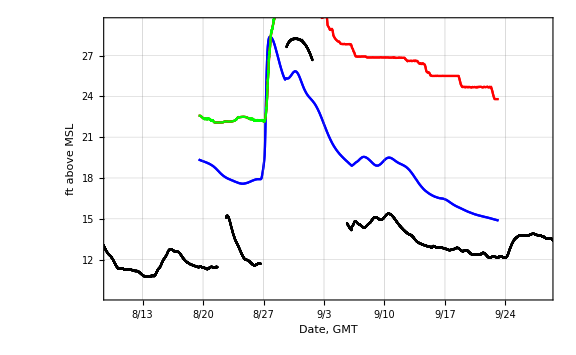

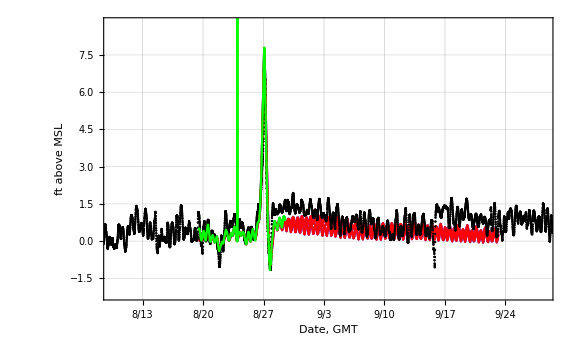

```mathematica
s4
s5
```

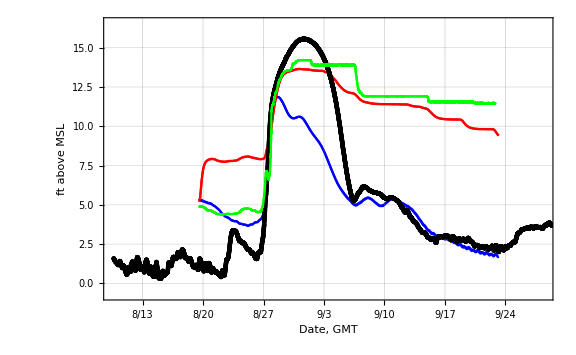

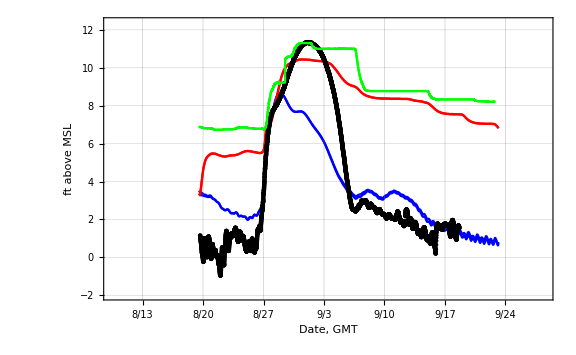

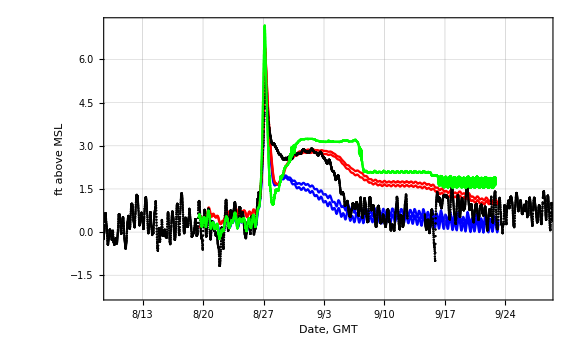

```mathematica
s1
s2
s22
s3
```